a (AU) | T (days) | a^3 | T^2 | k
0.25 | 46 | 0.015625 | 2116 | 135424.
0.5 | 125 | 0.125 | 15625 | 125000.
0.75 | 243 | 0.421875 | 59049 | 139968.
1 | 366 | 1 | 133956 | 133956

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

Mean k = 133590.000

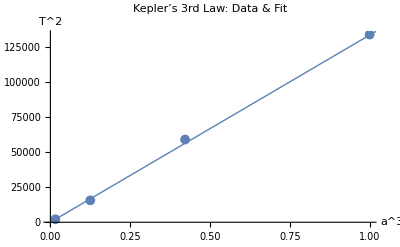

```mathematica
data={{0.25,46},{0.5,125},{0.75,243},{1,366}};


extended=Prepend[data/. {a_,T_}:>{a,T,a^3,T^2,T^2/a^3},{"a (AU)","T (days)","a^3","T^2","k"}];


Grid[extended,Frame->All,Spacings->{2,1},Alignment->Center]


meanK=Mean[extended[[2;;,5]]];
Print["Mean k = ",NumberForm[meanK,{5,3}]];


points=data/. {a_,T_}:>{a^3,T^2};


Show[ListPlot[points,PlotMarkers->{Automatic,10},AxesLabel->{"a^3","T^2"},PlotLabel->"Kepler’s 3rd Law: Data & Fit"],Plot[meanK x,{x,0,Max[points[[All,1]]]*1.1},PlotStyle->Thick]]
```